#### short-range coulomb force after Ewald partitioning into short and long range

```mathematica
ri={rix,riy,riz};
rj={rjx,rjy,rjz};
n={nx,ny,nz};
(*L is the box side length, S is the switching function for short-range energies/forces, n is the vector of cell integers, λ is the healing length, the characteristic length of the switching function *)
(* Keep in mind that the sum over i and j is between non-bonded atoms only for the short range force, as bonded atoms already experience the bond spring force which is supposed to subsume the Coulomb force between them, is subsume a word? idk 

the 1 / (4πϵ0) factor assumes the charges are in coulombs, in atomic units this factor is not present, I am using atomic units implicitly for everything including distances in bohr *)

energyExp=((qi*qj)/(((rix-rjx+nx*L)^2+(riy-rjy+ny*L)^2+(riz-rjz+nz*L)^2)^(1/2)))*Erfc[(((rix-rjx+nx*L)^2+(riy-rjy+ny*L)^2+(riz-rjz+nz*L)^2)^(1/2))/(√2*σ)];
R=(r-(rc-λ))/λ;
S=1+R^2*(2R-3);
```

```mathematica
Clear[r]
```

```mathematica
(*energyExp=(1/2) * ((qi*qj)/(r))*Erfc[r/(√2*σ)];*)
FullSimplify[energyExp*S]
```

(qi qj (r-rc)^2 (2 r-2 rc+3 λ) Erfc[r/(√2 σ)])/(2 r λ^3)

```mathematica
FullSimplify[energyExp*S]
```

(qi qj (rc-√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))^2 (-2 rc+2 √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+3 λ) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^3)

```mathematica
√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)=Ξ;
```

Set::write: Tag Sqrt in √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) is Protected.

```mathematica
D[energyExp*S,{ri}]
```

{-((ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) qi qj (L nx+rix-rjx) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)))/(√(2 π) ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ))+(qi qj ((2 (L nx+rix-rjx) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2)/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^3)+(2 (L nx+rix-rjx) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ) (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ))/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^2)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))-(qi qj (L nx+rix-rjx) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-((ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) qi qj (L ny+riy-rjy) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)))/(√(2 π) ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ))+(qi qj ((2 (L ny+riy-rjy) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2)/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^3)+(2 (L ny+riy-rjy) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ) (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ))/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^2)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))-(qi qj (L ny+riy-rjy) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-((ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) qi qj (L nz+riz-rjz) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)))/(√(2 π) ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ))+(qi qj ((2 (L nz+riz-rjz) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2)/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^3)+(2 (L nz+riz-rjz) (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ) (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ))/(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) λ^2)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 √((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))-(qi qj (L nz+riz-rjz) (1+1/λ^2(-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ)^2 (-3+(2 (-rc+√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)+λ))/λ)) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2))}

```mathematica
{-((ⅇ^(-ξ/(2 σ^2)) qi qj vx (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vx (-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vx (-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vx (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0),-((ⅇ^(-ξ/(2 σ^2)) qi qj vy (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vy(-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vy (-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vy(1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0),-((ⅇ^(-ξ/(2 σ^2)) qi qj vz (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vz(-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vz(-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vz(1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0)}
```

```mathematica
forceSimplified={-((ⅇ^(-ξ/(2 σ^2)) qi qj vx (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vx (-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vx (-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vx (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0),-((ⅇ^(-ξ/(2 σ^2)) qi qj vy (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vy(-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vy (-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vy(1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0),-((ⅇ^(-ξ/(2 σ^2)) qi qj vz (1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)))/(4 √2 π^(3/2) (ξ) ϵ0 σ))+(qi qj ((2 vz(-rc+Ξ+λ)^2)/(Ξ λ^3)+(2 vz(-rc+Ξ+λ) (-3+(2 (-rc+Ξ+λ))/λ))/(Ξ λ^2)) Erfc[Ξ/(√2 σ)])/(8 π Ξ ϵ0)-(qi qj vz(1+1/λ^2(-rc+Ξ+λ)^2 (-3+(2 (-rc+Ξ+λ))/λ)) Erfc[Ξ/(√2 σ)])/(8 π (ξ)^(3/2) ϵ0)};
```

```mathematica
FullSimplify[forceSimplified / (1 / (4π*ϵ0))]
```

{(qi qj vx ((ⅇ^(-ξ/(2 σ^2)) √(2/π) (2 rc-3 λ-2 Ξ) (rc-Ξ)^2)/(ξ σ)+((2 rc-3 λ-2 Ξ) (rc-Ξ)^2 Erfc[Ξ/(√2 σ)])/ξ^(3/2)+(6 (-rc+Ξ) (-rc+λ+Ξ) Erfc[Ξ/(√2 σ)])/Ξ^2))/(2 λ^3),(qi qj vy ((ⅇ^(-ξ/(2 σ^2)) √(2/π) (2 rc-3 λ-2 Ξ) (rc-Ξ)^2)/(ξ σ)+((2 rc-3 λ-2 Ξ) (rc-Ξ)^2 Erfc[Ξ/(√2 σ)])/ξ^(3/2)+(6 (-rc+Ξ) (-rc+λ+Ξ) Erfc[Ξ/(√2 σ)])/Ξ^2))/(2 λ^3),(qi qj vz ((ⅇ^(-ξ/(2 σ^2)) √(2/π) (2 rc-3 λ-2 Ξ) (rc-Ξ)^2)/(ξ σ)+((2 rc-3 λ-2 Ξ) (rc-Ξ)^2 Erfc[Ξ/(√2 σ)])/ξ^(3/2)+(6 (-rc+Ξ) (-rc+λ+Ξ) Erfc[Ξ/(√2 σ)])/Ξ^2))/(2 λ^3)}

```mathematica
forceClose=-D[energyExp,{rj}];
```

```mathematica
forceClose
```

{-(ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (L nx+rix-rjx))/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ)-(qi qj (L nx+rix-rjx) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-(ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (L ny+riy-rjy))/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ)-(qi qj (L ny+riy-rjy) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-(ⅇ^(-((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (L nz+riz-rjz))/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2) σ)-(qi qj (L nz+riz-rjz) Erfc[(√((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2))/(√2 σ)])/(((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2))}

```mathematica
energyExpBonded=1/2((qi*qj)/(((rix-rjx+nx*L)^2+(riy-rjy+ny*L)^2+(riz-rjz+nz*L)^2)^(1/2)));
forcesBonded=D[energyExpBonded,{ri}]
```

{-(qi qj (L nx+rix-rjx))/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-(qi qj (L ny+riy-rjy))/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2)),-(qi qj (L nz+riz-rjz))/(2 ((L nx+rix-rjx)^2+(L ny+riy-rjy)^2+(L nz+riz-rjz)^2)^(3/2))}

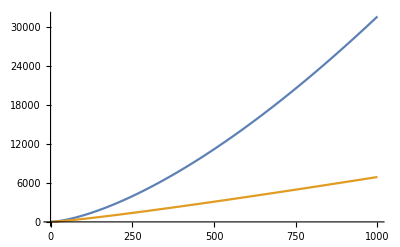

```mathematica
Plot[{n^(3/2),n*Log[n]},{n, 0, 1000}]
```

```mathematica
Conjugate[I*Exp[I*r]]
```

-ⅈ ⅇ^(-ⅈ Conjugate[r])

```mathematica
k={kx,ky,kz};
r={rx,ry,rz};
```

```mathematica
D[Exp[I*k.r], {r}]
```

{ⅈ ⅇ^(ⅈ (kx rx+ky ry+kz rz)) kx,ⅈ ⅇ^(ⅈ (kx rx+ky ry+kz rz)) ky,ⅈ ⅇ^(ⅈ (kx rx+ky ry+kz rz)) kz}

```mathematica
energyExp=
```

```mathematica
Clear[k,S];
k={kx,ky,kz};
rj={rjx,rjy,rjz};
```

```mathematica
D[Exp[-σ^2*(kx^2+ky^2+kz^2)/2]*qi*Exp[I*Dot[k*rj]],{rj}]
```

{{ⅈ ⅇ^(ⅈ kx rjx-1/2 (kx^2+ky^2+kz^2) σ^2) kx qi,0,0},{0,ⅈ ⅇ^(ⅈ ky rjy-1/2 (kx^2+ky^2+kz^2) σ^2) ky qi,0},{0,0,ⅈ ⅇ^(ⅈ kz rjz-1/2 (kx^2+ky^2+kz^2) σ^2) kz qi}}

```mathematica
D[qi*qj*Erf[((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(1/2)/(√2 σ)],{rj}]
```

{-(ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (rix-rjx))/(√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) σ),-(ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (riy-rjy))/(√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) σ),-(ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)/(2 σ^2)) √(2/π) qi qj (riz-rjz))/(√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) σ)}

```mathematica
rj
```

{rjx,rjy,rjz}

```mathematica
Clear[α]
```

```mathematica
exp=qi*qj*(Erf[α*((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(1/2)])/(((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(1/2));
-D[exp,{ri}]
```

{-(2 ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α^2) qi qj (rix-rjx) α)/(√π ((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2))+(qi qj (rix-rjx) Erf[√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α])/(((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(3/2)),-(2 ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α^2) qi qj (riy-rjy) α)/(√π ((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2))+(qi qj (riy-rjy) Erf[√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α])/(((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(3/2)),-(2 ⅇ^(-((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α^2) qi qj (riz-rjz) α)/(√π ((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2))+(qi qj (riz-rjz) Erf[√((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2) α])/(((rix-rjx)^2+(riy-rjy)^2+(riz-rjz)^2)^(3/2))}